# Mathématica Cours 3

## Rappel

## Q 1 :

```mathematica
f[x_]:=Sin[x]+Sin[2*x]
```

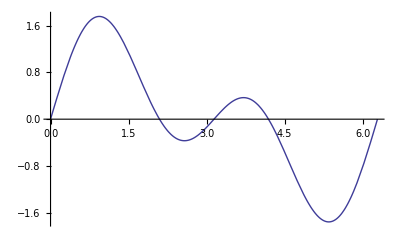

```mathematica
Plot[f[x],{x,0,2*Pi}]
```

## Q 2 :

```mathematica
g[n_]:=Table[Binomial[n,p],{p,0,n}]
```

```mathematica
g[5]
```

{1,5,10,10,5,1}

```mathematica
g[11]
```

{1,11,55,165,330,462,462,330,165,55,11,1}

## Q 3 :

```mathematica
Table[f[n],{n,0,10}]//TableForm
```

0
Sin[1]+Sin[2]
Sin[2]+Sin[4]
Sin[3]+Sin[6]
Sin[4]+Sin[8]
Sin[5]+Sin[10]
Sin[6]+Sin[12]
Sin[7]+Sin[14]
Sin[8]+Sin[16]
Sin[9]+Sin[18]
Sin[10]+Sin[20]

## Problème

## Q 4 :

```mathematica
f[x_]:=(1-x)/(2-x)
```

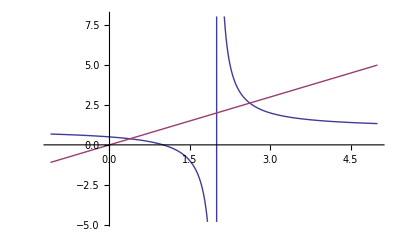

```mathematica
Plot[{f[x],x},{x,-1.1,5}]
```

```mathematica
u[0]=2.75;
u[n_]:=f[u[n-1]]
```

```mathematica
u[2]
```

4.

```mathematica
Table[u[k],{k,0,20}]//TableForm
```

2.75
2.33333
4.
1.5
-1.
0.666667
0.25
0.428571
0.363636
0.388889
0.37931
0.382979
0.381579
0.382114
0.38191
0.381988
0.381958
0.381969
0.381965
0.381966
0.381966

## Q 5 :

```mathematica
L1:=NestList[f,2.75,20]
```

## Q 6 :

```mathematica
g[x_]:={(x;x),(x;f[x])}
```

## Q 7 :

```mathematica
g[L1]//TableForm
```

2.75 | 2.33333 | 4. | 1.5 | -1. | 0.666667 | 0.25 | 0.428571 | 0.363636 | 0.388889 | 0.37931 | 0.382979 | 0.381579 | 0.382114 | 0.38191 | 0.381988 | 0.381958 | 0.381969 | 0.381965 | 0.381966 | 0.381966
2.33333 | 4. | 1.5 | -1. | 0.666667 | 0.25 | 0.428571 | 0.363636 | 0.388889 | 0.37931 | 0.382979 | 0.381579 | 0.382114 | 0.38191 | 0.381988 | 0.381958 | 0.381969 | 0.381965 | 0.381966 | 0.381966 | 0.381966

## Q 8 :

```mathematica
"Flatten[list] flattens out nested lists.
Flatten[list,n] flattens to level n."
```

## Q 9 :

```mathematica
L:=g[L1]
```

## Q 10 :

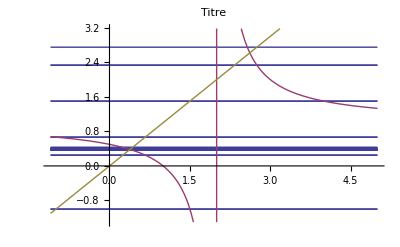

```mathematica
Show[Plot[{L,f[x],x},{x,-1.1,5}],PlotLabel->"Titre"]
```